INFINITE PRODUCT x/n) * sin(x*pi/n)

```mathematica
Quit[]
```

```mathematica
f[x1_, nm1_]:=Abs[Product[(x/n)*Sin[(x*Pi/n)],{n,2, nm1}]];
```

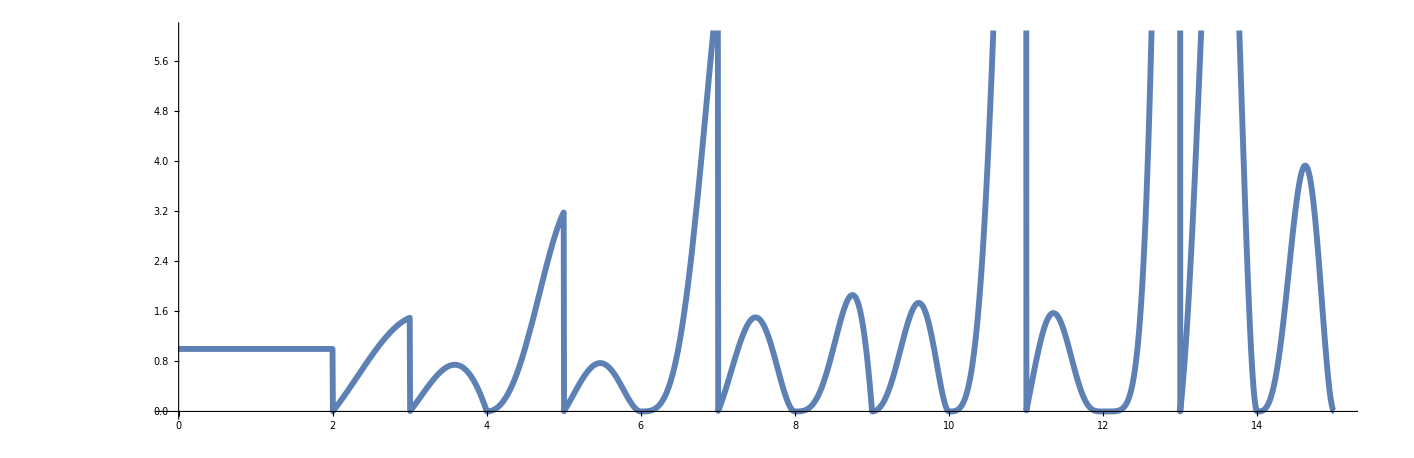

```mathematica
Plot[f[x1,x]//Evaluate,{x,0,15}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

LINEARIZED INFINITE PRODUCT

```mathematica
Y[xa_, ya_] := f[x1,x ]/f[x1,x]!
```

```mathematica
Plot[Y[xa,x]//Evaluate,{x,0,15}, PlotStyle-> Thickness[0.003],PlotRange ->  {0,1.5}, PlotStyle-> "SolarColors"]
```

NProduct::nplim: Limit of product x is not a number.

General::stop: Further output of NProduct::nplim will be suppressed during this calculation.